FittedModel[Piecewise[{{0.00854369, x<103.}, {5.88418×10^-15, x≥103.}, {0, True}}]]

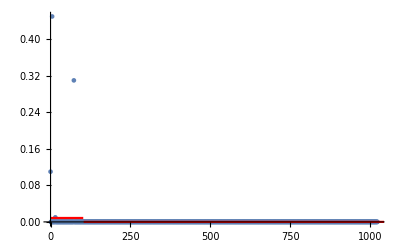

0.0241906

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
name := "regexSing-nq"
data :=Import[StringJoin["/Users/greg/Documents/School/Science_Research/workspace/ODRA-with-Enums/greg/queries/benchmarks-",name,".csv"], "Table", {"FieldSeparators" -> ";"}][[All,{1,3}]]
nlm = NonlinearModelFit[data, Piecewise[{{a,x<b},{c,x≥b}}],{a,{b,103},c},x]
Show[ListPlot[data],Plot[nlm[x],{x,0,2048},PlotStyle->Red]]
nlm["RSquared"]
```